Week 4: Singular Value decompositon

```mathematica
(*calculation the singular value decompostion*)
SingularValueDecomposition[{{1,2,3},{4,5,6},{7,8,9}}];
SingularValueDecomposition[{{1,2,3},{4,5,6},{7,8,9}}//N]
SingularValueDecomposition[{{1,2,3},{4,5,6},{7,8,9}}//N][[2]]//MatrixForm
```

{{{-0.214837,-0.887231,0.408248},{-0.520587,-0.249644,-0.816497},{-0.826338,0.387943,0.408248}},{{16.8481,0.,0.},{0.,1.06837,0.},{0.,0.,0.}},{{-0.479671,0.776691,0.408248},{-0.572368,0.0756865,-0.816497},{-0.665064,-0.625318,0.408248}}}

(16.8481 | 0. | 0.
0. | 1.06837 | 0.
0. | 0. | 0.)

```mathematica
(*solve LLS problems*)
```

Set::shape: Lists {u, w, v} and 16.9032 | 0. | 0.
0. | 1.04461 | 0.
0. | 0. | 0.0169902 are not the same shape.

{{{-0.214302,-0.897101,0.386374},{-0.518934,-0.230553,-0.823136},{-0.827516,0.376903,0.416128}},{{16.9032,0.,0.},{0.,1.04461,0.},{0.,0.,0.0169902}},{{-0.478172,0.78403,0.395788},{-0.570507,0.0653375,-0.81869},{-0.667737,-0.617274,0.416052}}}

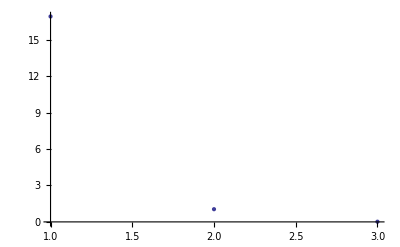

```mathematica
(* Dealing with rank deficient matrices*)
{u,w,v}=SingularValueDecomposition[{{1,2,3},{4,5,6},{7,8,9.1}}//N][[2]]//MatrixForm ;
(* Not a matrix that will behave well numerically. It is very sensitive to change in b values (A . x-> = b->) *)
(* Data contained in first column of u and first row of v is 16,000 times more important than 3rd col of u and row of v *)

(* DEALING WITH NEARLY RANK DEFICIENT MATRICIES: *)
(*Look at diagonal values of w and set all diagonal values less than some tolerance, tau, to 0 *)

(* Dealing with rank deficient matrices*)
{u,w,v}=SingularValueDecomposition[{{1,2,3},{4,5,6},{7,8,9.1}}//N]


ListPlot[Diagonal[w]]
```

-Graphics-

200

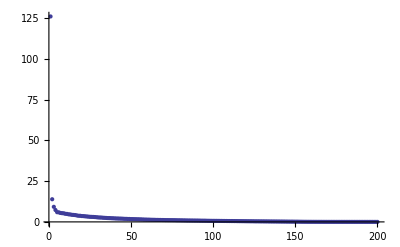

{«1»}

-Graphics-

ImageData::imginv: Expecting an image or graphics instead of image.

General::stop: Further output of ImageData :: imginv will be suppressed during this calculation.

Part::partw: Part 3 of SingularValueDecomposition[ImageData[image], 1] does not exist.

Image::imgarray: The specified argument ImageData[image] . 1 . Transpose[SingularValueDecomposition[ImageData[image], 1] ⟦ 3 ⟧] should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
(*Make low rank approximations of your data*)
image=Import["ExampleData/ocelot.jpg"]
MatrixRank[ImageData[image]]
ImageData[image];
{u,w,v}=SingularValueDecomposition[ImageData[image]];
ListPlot[Diagonal[w],PlotRange->Full]
{u2,w2,v2}=SingularValueDecomposition[ImageData[image],50](* First 50 singular values *)
Image[u2.w2.Transpose[v2]] (* Reconstruct a but with the first 50 singular values *)
Manipulate[Image[SingularValueDecomposition[ImageData[image],i][[1]].SingularValueDecomposition[ImageData[image],i][[2]].Transpose[SingularValueDecomposition[ImageData[image],i][[3]]]],{i,1,200,1}]
```

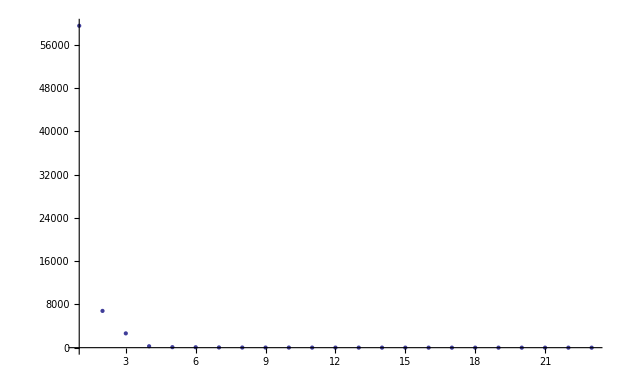

{Point[{12.9,15.9,18.8}],Point[{29.2,33.9,38.7}],Point[{25.9,29.1,32.3}],Point[{30.8,37.7,44.6}],Point[{23.7,30.,36.2}],Point[{14.2,15.7,17.3}],Point[{19.9,20.8,21.7}],Point[{22.6,23.7,24.9}],Point[{26.3,26.3,26.3}],Point[{33.,34.7,36.3}],Point[{37.5,40.1,42.7}],Point[{8.5,13.4,18.3}],Point[{11.4,11.4,11.4}],Point[{13.4,15.1,16.8}],Point[{13.4,15.9,18.4}],Point[{18.,18.8,19.6}],Point[{18.4,18.4,18.4}],Point[{14.5,15.8,17.1}],Point[{29.5,29.5,29.5}],Point[{7.9,9.2,10.6}],Point[{8.4,11.3,14.2}],Point[{11.9,13.3,14.7}],Point[{14.8,15.6,16.4}],Point[{18.5,25.8,33.1}],Point[{7.9,12.2,16.5}],Point[{17.5,19.3,21.2}],Point[{6.9,7.4,7.9}],Point[{8.4,10.1,11.9}],Point[{10.4,11.3,12.2}],Point[{10.8,15.9,21.}],Point[{12.8,14.,15.2}],Point[{15.6,20.2,24.8}],Point[{20.1,20.9,21.7}],Point[{6.7,8.4,10.}],Point[{11.5,12.5,13.5}],Point[{17.,19.8,22.7}],Point[{8.4,12.1,15.8}],Point[{13.8,17.5,21.2}],Point[{6.8,8.,9.2}],Point[{9.,10.,11.}],Point[{9.1,10.,11.}],Point[{12.4,13.9,15.3}],Point[{45.4,47.9,50.4}],Point[{27.5,28.,28.4}],Point[{34.7,35.2,35.6}],Point[{33.3,34.3,35.3}],Point[{34.4,36.1,37.8}],Point[{7.4,8.3,9.1}],Point[{10.9,11.6,12.3}],Point[{14.3,16.5,18.7}],Point[{29.,31.9,34.9}],Point[{43.8,61.9,80.}],Point[{13.3,14.1,15.}],Point[{14.9,14.9,14.9}],Point[{7.7,10.3,12.9}],Point[{22.4,26.1,29.9}],Point[{8.7,11.8,14.9}],Point[{13.,15.7,18.3}],Point[{21.,21.5,22.}],Point[{13.,13.5,14.}],Point[{14.2,16.3,18.4}],Point[{19.5,20.7,21.9}],Point[{11.4,14.4,17.4}],Point[{8.2,9.,9.9}],Point[{9.4,11.1,12.8}],Point[{14.,17.7,21.4}],Point[{15.4,18.5,21.6}],Point[{19.4,24.4,29.4}],Point[{20.3,28.7,37.1}],Point[{9.2,11.1,12.9}],Point[{7.3,8.4,9.5}],Point[{10.5,10.9,11.3}],Point[{16.3,19.5,22.7}],Point[{7.3,8.6,10.}],Point[{7.8,9.8,11.8}],Point[{14.2,18.4,22.6}],Point[{15.2,18.2,21.2}],Point[{8.7,9.1,9.5}],Point[{17.6,20.,22.4}],Point[{22.9,23.3,23.7}],Point[{21.8,22.7,23.5}],Point[{24.8,26.7,28.5}]}

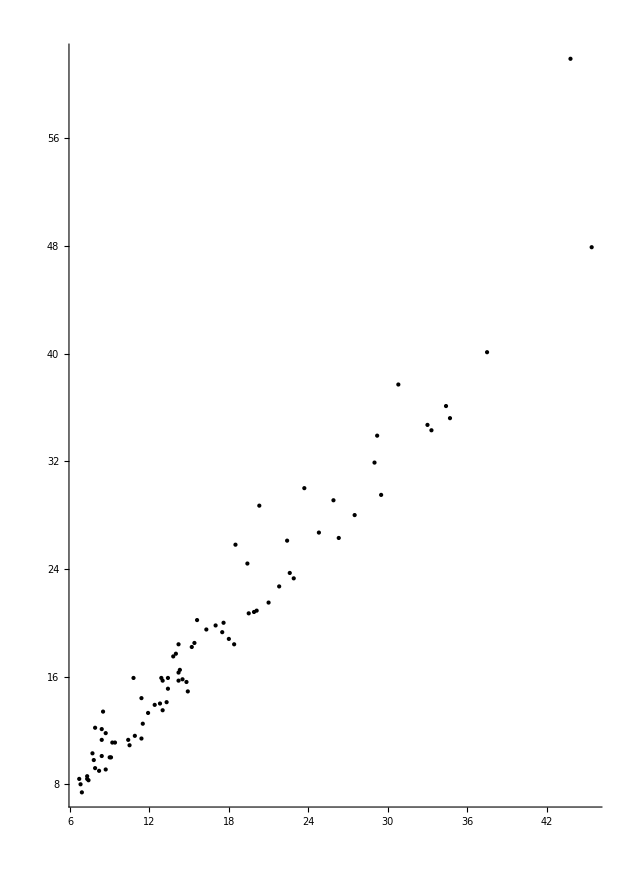

-Graphics3D-

```mathematica
(*Dimensional reduction of data*)
rawdata=Import["http://www.amstat.org/publications/jse/datasets/93cars.dat.txt","Lines"];
partdata=Partition[rawdata,2];
paddedsec=StringJoin[" ",#]& /@partdata[[All,2]];
predata=StringJoin[#[[1]],#[[2]]]& /@ Transpose[{partdata[[All,1]],paddedsec}] // StringSplit;
nums=Map[If[#≠"*",ToExpression[#],#]&,predata[[All,4;;]],{2}];
data=Flatten[#] &/@Transpose[{predata[[All,1;;3]],nums}];
data2=Cases[data,Except[{__,"*",___}]];
data3=Map[ToExpression,data2[[All,4;;]],{2}];

{u,w,v}=SingularValueDecomposition[data3]; 
ListPlot[Diagonal[w],PlotRange->All]
dimred2=u.w.(Transpose[v][[All,1;;2]]); (* First two cols *)
dimred3=u.w.(Transpose[v][[All,1;;3]]); (* First three cols *)
graphdat2=Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{data2[[All,1;;3]],dimred2}];
graphdat3=Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{data2[[All,1;;3]],dimred3}]
Graphics[graphdat2,Axes->True,AxesOrigin->{0,0}]
Graphics3D[graphdat3,Axes->True,AxesOrigin->{0,0,0}]
```